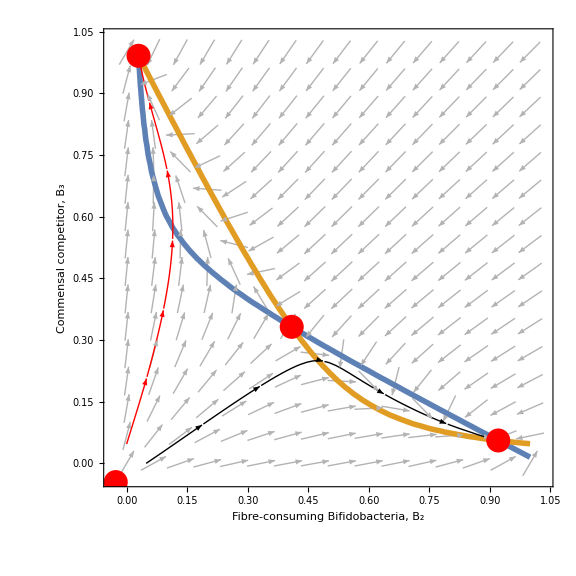

```mathematica
(* plot nullcline b2 b3 *)
r=1;k=1000; α=2;Subscript[f, 3]=50/k;Subscript[f, 2]=30/k;
f[B_,C_]:=r B - r B^2-r α B C+Subscript[f, 2];
g[B_,C_]:= r C - r C^2-r α B C+Subscript[f, 3];
vp=VectorPlot[{f[B,C],g[B,C]},{B,0,1},{C,0,1},VectorScale-> {0.05,0.9,None},Axes->True,AxesLabel->{B,C},VectorPoints->16,VectorStyle->{GrayLevel[0.7]}];
cp=ContourPlot[{f[B,C]==0,g[B,C]==0},{B,0,1},{C,0,1},ContourStyle->Directive[AbsoluteThickness[4]]];
sp=StreamPlot[{f[B,C],g[B,C]},{B,0,1},{C,0,1},StreamPoints->{{{{50/k,1/k},Black},{{1/k,50/k},Red}}},StreamScale->Medium];
ptRules=NSolve[{f[B,C]==0,g[B,C]==0},{B,C}];
p2=Show[vp,cp,sp,Graphics[{Red,PointSize[0.03],Point[{B,C}]/.ptRules}],FrameLabel->{{HoldForm["Commensal competitor, B_3"],None},{HoldForm["Fibre-consuming Bifidobacteria, B_2"],None}},PlotLabel->None,LabelStyle->{24,GrayLevel[0]},ImageSize->Large]
```

```mathematica
(* plot nullcline b2 b3*)
r=1;k=1000; α=0.5;Subscript[f, 3]=50/k;Subscript[f, 2]=30/k;
f[B_,C_]:=r B - r B^2-r α B C+Subscript[f, 2];
g[B_,C_]:= r C - r C^2-r α B C+Subscript[f, 3];
vp=VectorPlot[{f[B,C],g[B,C]},{B,-0.01,1},{C,-0.010,1},VectorScale->{0.05,0.9,None},Axes->True,AxesLabel->{B,C},VectorPoints->16,VectorStyle->{GrayLevel[0.7]}];
cp=ContourPlot[{f[B,C]==0,g[B,C]==0},{B,0,1},{C,0,1},ContourStyle->Directive[AbsoluteThickness[4]]];
sp=StreamPlot[{f[B,C],g[B,C]},{B,-0.01,1},{C,-0.01,1},StreamPoints->{{{{50/k,1/k},Black},{{1/k,50/k},Red}}},StreamScale->Medium];
ptRules=NSolve[{f[B,C]==0,g[B,C]==0},{B,C}];
p1=Show[vp,cp,sp,Graphics[{Red,PointSize[0.03],Point[{B,C}]/.ptRules}],FrameLabel->{{HoldForm["Commensal competitor, B_3"],None},{HoldForm["Fibre-consuming Bifidobacteria, B_2"],None}},PlotLabel->None,LabelStyle->{24,GrayLevel[0]},ImageSize->Large]
```